# Nanobot Theory : Data Analysis and Plotting

#### Yibin Jiang, Abhishek Sharma Cronin Lab University of Glasgow

```mathematica
baseDirectory=NotebookDirectory[];
```

```mathematica
scaleFac = 1.0;(* Scaling Factor for dipole coordinates *)
oldstructure=1/scaleFac Import[baseDirectory<>"/data_Au@Ag_Octahedra/octahedra_core.csv"];
newstructure=1/scaleFac Import[baseDirectory<>"/data_Au@Ag_Octahedra/octahedra_overall.csv"];
```

```mathematica
Dimensions/@{oldstructure,newstructure}
```

{{3303,3},{4089,3}}

```mathematica
npImage = Graphics3D[{{Yellow,Opacity[0.5],Sphere[oldstructure,1/2]},{Blue,Opacity[0.4],Sphere[Complement[newstructure,oldstructure],1/2]}},Boxed->True,ViewProjection->"Orthographic",ViewPoint->{2,-2,1},ImageSize->{300,300}]
```

-Graphics3D-

```mathematica
Export[baseDirectory<>"np_image.png",npImage,ImageResolution-> 300]
```

Z:\group\Yibin Jiang\Papers\Nanobot_Theory\Code\Au@Ag octahedra\np_image.png

```mathematica
dipoleLength=Quantity[1.0,"nm"];
```

```mathematica
d=QuantityMagnitude[10^-3 dipoleLength]; (* For plotting 10^-3 is a scaling factor *)
```

```mathematica
deleteIndex = 1+Flatten@IntegerPart@N@Import[baseDirectory<>"/data_Au@Ag_Octahedra/exp1/random_delete_sequence_0.csv"];
deleteIndex=Table[{i},{i,deleteIndex}];
data=Import[baseDirectory<>"//data_Au@Ag_Octahedra/exp1/data_random_seed_0.csv"];
```

```mathematica
wavelength = Table[0.39+0.01*i,{i,51}];
```

```mathematica
plotUVVis[index_]:= Block[{Au,structure,reffi,tempData,intp,plot1,plot2,fig},
Au=Delete[newstructure,deleteIndex⟦;;index⟧];
structure=Graphics3D[{{Yellow,Opacity[0.5],Sphere[oldstructure,1/2]},{Blue,Opacity[0.4],Sphere[Complement[Au,oldstructure],1/2]}},Boxed->False,ViewProjection->"Orthographic",ViewPoint->{2,-2,1},ImageSize->{300,300}];
reffi=(3/(4π)d^3 Length@Au )^(1/3);
tempData=Transpose[{1000*wavelength,data⟦All,1+index⟧/(π reffi^2)}];
intp=Interpolation[tempData,InterpolationOrder->2];
plot1=Plot[intp[x],{x,400,650},PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotRange->{0,12}];
plot2=ListPlot[tempData,PlotStyle->{Black,PointSize[0.02]},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]}];
fig=Show[{plot1,plot2},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame-> True,FrameLabel->{"Wavelength (nm)","Extinction"},AspectRatio->1,ImageSize->300,PlotRange->{0,1.8}];{structure,fig}]
```

```mathematica
Monitor[Table[Block[{p1,p2,output},
p1=plotUVVis[index]⟦1⟧;p2=plotUVVis[index]⟦2⟧;output=Show[{p2,Graphics[Inset[p1,{800,1.2},Automatic,Scaled[0.8]]]}];
Export[baseDirectory<>"Combined/random/0/"<>ToString[786-index]<>".png",output,ImageResolution-> 300] ;
Export[baseDirectory<>"Combined/random/0/"<>"shape"<>ToString[786-index]<>".png",p1,ImageResolution-> 300]],
{index,0,Length[deleteIndex]}];,index]
```

```mathematica
restylePlot2[p_,op:OptionsPattern[ListLinePlot]]:=ListLinePlot[Cases[Normal@p,Line[x__]:>x,∞],op,Options[p]];
```

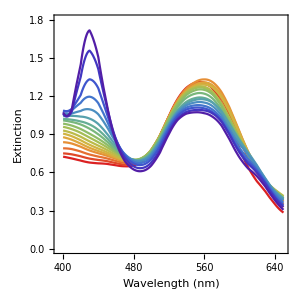

Z:\group\Yibin Jiang\Papers\Nanobot_Theory\Code\Au@Ag octahedra\/Random0-2.png

```mathematica
plots = Flatten@{Table[plotUVVis[i]⟦2⟧,{i,786,0,-50}],plotUVVis[0]⟦2⟧};
f = restylePlot2[plots,PlotStyle->Reverse@Table[ColorData["Rainbow"][i],{i,0,1,1/Length[plots]}],FrameStyle->Directive[16,FontColor->Black],PlotRange->{0,1.8},AspectRatio->1,ImageSize->300,Frame-> True,FrameLabel->{"Wavelength (nm)","Extinction"}]
Export[NotebookDirectory[]<>"/Random0-2.png",f,ImageResolution->300]
```